Computations on case 2: Fixed sample size in period 1
Set (and simplify) conditions

```mathematica
r11= N1/NT - r01
```

N1/NT-r01

```mathematica
cond1 = r01+r11+r02+r12+r22+r03+r23
```

N1/NT+r02+r03+r12+r22+r23

```mathematica
Solve[r01+r11+r02+r12+r22+r03+r23==1, r23]
```

{{r23→(-N1+NT-NT r02-NT r03-NT r12-NT r22)/NT}}

```mathematica
r23=(-N1+NT-NT r02-NT r03-NT r12-NT r22)/NT
```

(-N1+NT-NT r02-NT r03-NT r12-NT r22)/NT

```mathematica
Simplify[r23]
```

-(N1+NT (-1+r02+r03+r12+r22))/NT

Define terms to optimise
Note: sigma*term1^(-1)/N is the variance of the estimator of effect 1 (analogously sigma*term2^(-1)/N for effect 2). But since sigma and N are fixed, we simply work on term1 and term2 expressions.

```mathematica
term1=(r11*r01/(r11+r01))+(r12*r02/(r12+r02))
```

(NT (N1/NT-r01) r01)/N1+(r02 r12)/(r02+r12)

```mathematica
term1=FullSimplify[term1]
```

r01-(NT r01^2)/N1+(r02 r12)/(r02+r12)

```mathematica
term2=(r22*r02/(r22+r02))+(r23*r03/(r23+r03))
```

(r02 r22)/(r02+r22)+(r03 (-N1+NT-NT r02-NT r03-NT r12-NT r22))/(NT (r03+(-N1+NT-NT r02-NT r03-NT r12-NT r22)/NT))

```mathematica
term2=FullSimplify[term2]
```

r03+(r02 r22)/(r02+r22)+(NT r03^2)/(N1+NT (-1+r02+r12+r22))

```mathematica
sol=Solve[term1-term2==0, r01]
```

{{r01→-(N1 (-1-√(1+(4 NT (-r03+(r02 r12)/(r02+r12)-(r02 r22)/(r02+r22)-(NT r03^2)/(N1-NT+NT r02+NT r12+NT r22)))/N1)))/(2 NT)},{r01→-(N1 (-1+√(1+(4 NT (-r03+(r02 r12)/(r02+r12)-(r02 r22)/(r02+r22)-(NT r03^2)/(N1-NT+NT r02+NT r12+NT r22)))/N1)))/(2 NT)}}

```mathematica
r01 = -(N1 (-1-√(1+(4 NT (-r03+(r02 r12)/(r02+r12)-(r02 r22)/(r02+r22)-(NT r03^2)/(N1-NT+NT r02+NT r12+NT r22)))/N1)))/(2 NT)
```

-(N1 (-1-√(1+(4 NT (-r03+(r02 r12)/(r02+r12)-(r02 r22)/(r02+r22)-(NT r03^2)/(N1-NT+NT r02+NT r12+NT r22)))/N1)))/(2 NT)

```mathematica
term = FullSimplify[term1]
```

r03+(r02 r22)/(r02+r22)+(NT r03^2)/(N1+NT (-1+r02+r12+r22))

Optimisation under equal variances with respect to r02

```mathematica
Solve[D[1/term,r02]==0,r02]
```

{{r02→-(r22 (N1-NT-NT r03+NT r12+NT r22))/(NT (-r03+r22))},{r02→-(r22 (N1-NT+NT r03+NT r12+NT r22))/(NT (r03+r22))}}

```mathematica
r02=-(r22 (N1-NT-NT r03+NT r12+NT r22))/(NT (-r03+r22))
```

-(r22 (N1-NT-NT r03+NT r12+NT r22))/(NT (-r03+r22))

```mathematica
FullSimplify[1/term]
```

(N1+NT (-1+r12))/(N1 (r03+r22)+NT (r03^2+r03 (-1+r12-2 r22)+r22 (-1+r12+r22)))

Assume r22=r12, and optimize with respect to r03

```mathematica
FullSimplify[(1/term)/.{r22->r12} ]
```

(N1+NT (-1+r12))/(N1 (r03+r12)+NT (r03^2-r03 (1+r12)+r12 (-1+2 r12)))

```mathematica
Solve[D[FullSimplify[(1/term)/.{r22->r12} ],r03]==0,r03]
```

{{r03→(-N1+NT+NT r12)/(2 NT)}}

```mathematica
v= FullSimplify[(1/term)/.{r22->r12,r03->(-N1+NT+NT r12)/(2 NT)} ]
```

(4 NT)/(-N1+NT+7 NT r12)

```mathematica
Plot3D[v /.NT->100, {N1,0,100}, {r12,0,1}]
```

-Graphics3D-

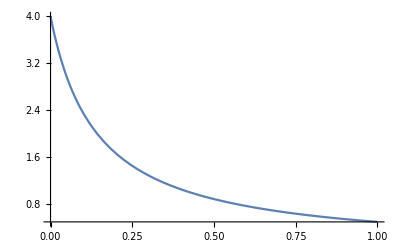

```mathematica
Plot[v=(4 NT)/(-N1+NT+7 NT r12) /.{NT->100,N1->1/100}, {r12,0,1}]
```